# ChristopherWolfram/CuneiformTools

[EXPERIMENTAL] Tools for cuneiform data retrieval

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Symbols"

"OraccData.nb"DocumentationEnglishReferencePagesSymbolsOraccData.nb

"Tutorials"

"Kernel"

"CuneiformTools.wl"KernelCuneiformTools.wl

"Oracc.wl"KernelOracc.wl

"Notes"

"oraccImporter.nb"NotesoraccImporter.nb

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

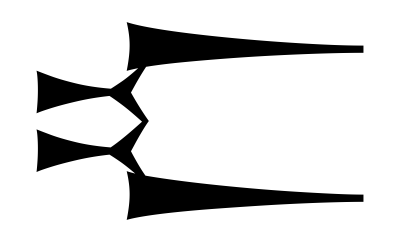
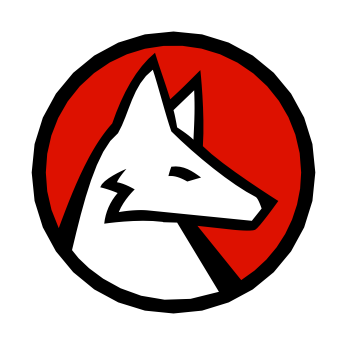

```mathematica
Graphics[{
BoundaryDiscretizeGraphics[Text["𒉒"],_Text],
Inset[,{1.8,0},Automatic,4.5]
}]
```

### Basic Description

CuneiformTools provides tools for retrieving, representing, and processing cuneiform text. However, it is at a very early state of development, and currently only provides functionality for importing from Oracc.

### Details

Makes it possible to get data from the Oracc API.

### Primary Context

ChristopherWolfram`CuneiformTools`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["ChristopherWolfram`CuneiformTools`"];
```

### Basic Examples

Get the translation of an Astronomical Diary text:

```mathematica
OraccData[{"adsd","adart3"},"X300760"]
```

[... Venus was] 6 fingers [above] Mars. Ni[ght ...]
[... Ve]nus was 3 cubits below β Capricorni. Night [...]
[... Jupiter was] 2 cubits below η Tauri. Night of the 11th, beginning of the night, the moo[n ...]
[...] last part of the night, Mars was 2 .bd cubits below β Capricorni. Night of the 11+[xth, ...]
[...] when it began from the north, in 8° of night [it made] 3 fingers [...]
[...] Jupiter and Sirius stood there [...]
[...] the moon being .bd cubit to [...]

Get its transliteration:

```mathematica
OraccData[{"adsd","adart3"},"X300760","Transliteration"]
```

[... dele-bat e] AN 6 SI ⸢GE₆⸣ [...]
[... dele]-bat SIG SI-MAŠ₂ 3 KUŠ₃ GE₆ [...]
[... MUL₂.BABBAR] SIG MUL₂.MUL₂ 2 KUŠ₃ GE₆ 11 SAG GE₆ ⸢sin⸣ [...]
[...] ina ZALAG₂ AN SIG SI-MAŠ₂ 2 1/2 KUŠ₃ GE₆ 11+[n ...]
[...] TA SI ki TAB-u₂ ina 8 GE₆ 3 SI [...]
[...] MUL₂.BABBAR u MUL₂.KAK.SI.SA₂ GUB.⸢MEŠ⸣ [...]
[...] sin 1/2 KUŠ₃ ana [...]

## Source & Additional Information

### Creator

Christopher Wolfram

### Source Control Repository

https://github.com/chriswolfram/CuneiformTools

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

cuneiform

ancient text

Babylonian

digital humanities

computational history

history

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

GitHub - chriswolfram/CuneiformTools

### Links

Oracc: The Open Richly Annotated Cuneiform Corpus

### Compatibility

#### Wolfram Language Version

14+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.